# Hyperboloidal slices close to spatial infinity

5 July 2022

```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

```mathematica
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{mathrsfs}\\DeclareSymbolFontAlphabet{\\mathrsfs}{rsfs}
\\newcommand{\\scri}{\\mathrsfs{I}}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{mathrsfs}\DeclareSymbolFontAlphabet{\mathrsfs}{rsfs}
\newcommand{\scri}{\mathrsfs{I}}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
MaTeX["\\scri^+"]
```

-Graphics-

## Coordinate changes and slices plots

Pretty printing

```mathematica
uphys/:MakeBoxes[uphys,StandardForm]:="ũ";
vphys/:MakeBoxes[vphys,StandardForm]:="ṽ";
tphys/:MakeBoxes[tphys,StandardForm]:="t̃";
rphys/:MakeBoxes[rphys,StandardForm]:="r̃";
tpen/:MakeBoxes[tpen,StandardForm]:="T";
rpen/:MakeBoxes[rpen,StandardForm]:="ψ";
thyp/:MakeBoxes[thyp,StandardForm]:="t";
rhyp/:MakeBoxes[rhyp,StandardForm]:="r";
Omega/:MakeBoxes[Omega,StandardForm]:="Ω";
height/:MakeBoxes[height,StandardForm]:="h";
tau/:MakeBoxes[tau,StandardForm]:="τ";
rho/:MakeBoxes[rho,StandardForm]:="ρ";
```

#### Physical polar to Physical null coordinates

```mathematica
uvphysTotrphys={uphys==tphys-rphys,vphys==rphys+tphys}
```

{ũ==-r̃+t̃,ṽ==r̃+t̃}

```mathematica
trphystouvphys={tphys==(uphys+vphys)/2,rphys==(vphys-uphys)/2}
```

{t̃==(ũ+ṽ)/2,r̃==1/2 (-ũ+ṽ)}

#### Penrose - Diagram coordinates

```mathematica
trphysTopen={tphys==Sin[tpen]/(Cos[tpen]+Cos[rpen]),rphys==Sin[rpen]/(Cos[tpen]+Cos[rpen])}
```

{t̃==Sin[T]/(Cos[ψ]+Cos[T]),r̃==Sin[ψ]/(Cos[ψ]+Cos[T])}

```mathematica
trpenTophys={tpen==ArcTan[tphys+rphys]+ArcTan[tphys-rphys],rpen==ArcTan[tphys+rphys]-ArcTan[tphys-rphys]}
```

{T==-ArcTan[r̃-t̃]+ArcTan[r̃+t̃],ψ==ArcTan[r̃-t̃]+ArcTan[r̃+t̃]}

```mathematica
trpenTophys={tpen==ArcTan[2tphys/(1-(tphys^2-rphys^2))],rpen==ArcTan[2rphys/(1+(tphys^2-rphys^2))]}
```

{T==ArcTan[(2 t̃)/(1+(r̃)^2-(t̃)^2)],ψ==ArcTan[(2 r̃)/(1-(r̃)^2+(t̃)^2)]}

Sanity check

```mathematica
trphysTopen
%/.{trpenTophys/.Equal->Rule}//Flatten
%//PowerExpand//Together//Together//FullSimplify
```

{t̃==Sin[T]/(Cos[ψ]+Cos[T]),r̃==Sin[ψ]/(Cos[ψ]+Cos[T])}

{t̃==(2 t̃)/((1+(r̃)^2-(t̃)^2) √(1+(4 (t̃)^2)/((1+(r̃)^2-(t̃)^2)^2)) (1/(√(1+(4 (t̃)^2)/((1+(r̃)^2-(t̃)^2)^2)))+1/(√(1+(4 (r̃)^2)/((1-(r̃)^2+(t̃)^2)^2))))),r̃==(2 r̃)/((1-(r̃)^2+(t̃)^2) √(1+(4 (r̃)^2)/((1-(r̃)^2+(t̃)^2)^2)) (1/(√(1+(4 (t̃)^2)/((1+(r̃)^2-(t̃)^2)^2)))+1/(√(1+(4 (r̃)^2)/((1-(r̃)^2+(t̃)^2)^2)))))}

{t̃==-(2 t̃ √(1+(4 (r̃)^2)/((1-(r̃)^2+(t̃)^2)^2)))/((-1-(r̃)^2+(t̃)^2) (√(1+(4 (t̃)^2)/((1+(r̃)^2-(t̃)^2)^2))+√(1+(4 (r̃)^2)/((1-(r̃)^2+(t̃)^2)^2)))),r̃==-(2 r̃ √(1+(4 (t̃)^2)/((1+(r̃)^2-(t̃)^2)^2)))/((-1+(r̃)^2-(t̃)^2) (√(1+(4 (t̃)^2)/((1+(r̃)^2-(t̃)^2)^2))+√(1+(4 (r̃)^2)/((1-(r̃)^2+(t̃)^2)^2))))}

#### Cauchy Slices plot of Penrose Diagram

{T==π-ψ}

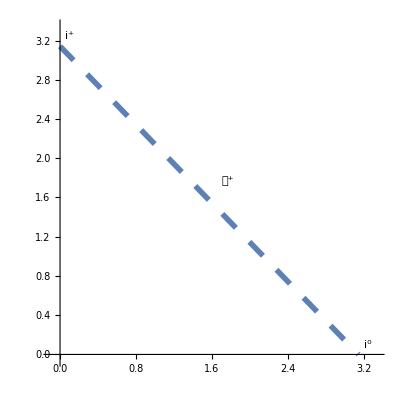

```mathematica
FutureNullInfinityPen={tpen==Pi-rpen}
FutureNullInfinityPlot=Plot[Pi-rpen,{rpen,0,Pi},PlotRange->{{-0.1,Pi+0.2},{-0.05,Pi+0.2}},AspectRatio->1,PlotStyle->{Thickness[0.01],Dashing[Large]},Epilog->{Text[Style["𝒥^+",Large],{Pi/2+0.2,Pi/2+0.2}],Text[Style["i^0",Large],{Pi+0.1,0.1}],Text[Style["i^+",Large],{0.1,Pi+0.1}]}]
```

{T==π-ψ}

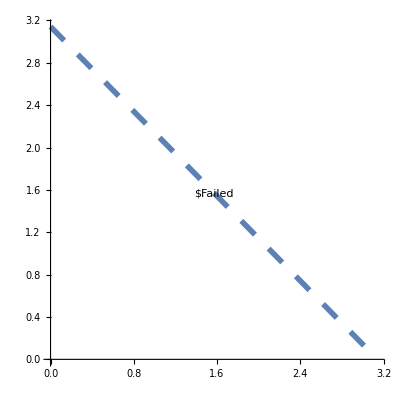

```mathematica
FutureNullInfinityPen={tpen==Pi-rpen}
FutureNullInfinityPlot=Plot[Pi-rpen,{rpen,0,Pi},PlotRange->{{0,Pi},{0,Pi}},AspectRatio->1,PlotStyle->{Thickness[0.01],Dashing[Large]},Epilog->Text[Style[ToExpression["𝒥 ^{+}",TeXForm,HoldForm],Large],{Pi/2,Pi/2}]]
```

In relativity the vertical axis is time and the horizontal axis is space .    In standard plotting tools we give first horizontal and then vertical .   In relativity coordinates are given first giving time and then space .

```mathematica
RelativisticPlotToMathematicaPlotOrder[x_]:=Flatten[{x[[2]],x[[1]]}]
```

Functions to plot

```mathematica
CauchySurfacesInPenrose[tphys_]:=Evaluate[{trpenTophys[[1,2]],trpenTophys[[2,2]]}]
```

The time symmetric Cauchy hypersurface is  t̃ = 0.

```mathematica
RelativisticPlotToMathematicaPlotOrder[CauchySurfacesInPenrose[0]]
```

{ArcTan[(2 r̃)/(1-(r̃)^2)],0}

```mathematica
ListOfCauchySlices={RelativisticPlotToMathematicaPlotOrder[CauchySurfacesInPenrose[0]],RelativisticPlotToMathematicaPlotOrder[CauchySurfacesInPenrose[0.1]],RelativisticPlotToMathematicaPlotOrder[CauchySurfacesInPenrose[0.5]],RelativisticPlotToMathematicaPlotOrder[CauchySurfacesInPenrose[1.5]]};
```

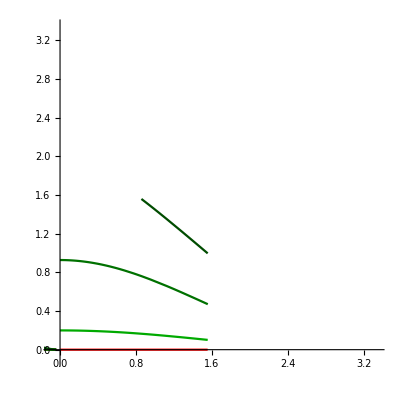

```mathematica
CauchySurfacesPenrosePlot=ParametricPlot[ListOfCauchySlices,{rphys,0,50},PlotRange->{{-0.1,Pi+0.2},{-0.1,Pi+0.2}},AspectRatio->1,PlotStyle->{Red,Darker[Green],Darker[Darker[Green]],Darker[Darker[Darker[Green]]]}]
```

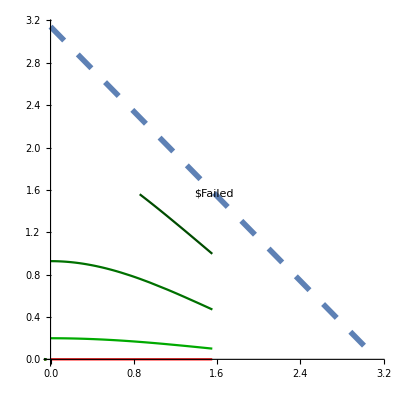

```mathematica
Show[FutureNullInfinityPlot,CauchySurfacesPenrosePlot]
```

Friedrich to Physical

```mathematica
FtoPhys={tau==tphys/rphys,rho==rphys/(rphys^2-tphys^2)}
```

{τ==(t̃)/(r̃),ρ==(r̃)/((r̃)^2-(t̃)^2)}

```mathematica
PhysToF=Flatten@Solve[FtoPhys,{tphys,rphys}]/.Rule->Equal
```

{t̃==-τ/(ρ (-1+τ^2)),r̃==-1/(ρ (-1+τ^2))}

Sanity Check

```mathematica
FtoPhys
%/.{PhysToF/.Equal->Rule};
Flatten@%;
%//Simplify
```

{τ==(t̃)/(r̃),ρ==(r̃)/((r̃)^2-(t̃)^2)}

{True,True}

Checking spatial orientation ---conventional but needed for clarity.

Positive  physical radius should correspond to positive rho coordinate

```mathematica
PhysToF
%[[2]]
%/.{tau->0}
```

{t̃==-τ/(ρ (-1+τ^2)),r̃==-1/(ρ (-1+τ^2))}

r̃==-1/(ρ (-1+τ^2))

r̃==1/ρ

#### Cauchy Slices in Friedrich Diagram

Checking  time orientation ---conventional but needed for clarity.

Location of future null infinity

```mathematica
trpenTophys;
%/.{PhysToF/.Equal->Rule};
Flatten@%;
%//Simplify;
(Solve[%,{tpen,rpen}]//Flatten)/.Rule->Equal;
trpentoF=%
```

{T==ArcTan[(2 ρ τ)/(1+ρ^2-ρ^2 τ^2)],ψ==-ArcTan[(2 ρ)/(1+ρ^2 (-1+τ^2))]}

In Penrose - digram coordinate future null infinity is located at

```mathematica
FutureNullInfinityPen
```

{T==π-ψ}

Checking this corresponds to τ = 1

```mathematica
tpen+rpen
%/.(trpentoF/.Equal->Rule)
Limit[%,tau->1,Direction->"FromBelow"]
Refine[%,rho>0]
```

ψ+T

ArcTan[(2 ρ τ)/(1+ρ^2-ρ^2 τ^2)]-ArcTan[(2 ρ)/(1+ρ^2 (-1+τ^2))]

0

0

Diagrams

```mathematica
FutureNullInfinityFri={tau==1}
```

{τ==1}

```mathematica
spinflineStyle={Thickness[0.01],Black,Dashed};
```

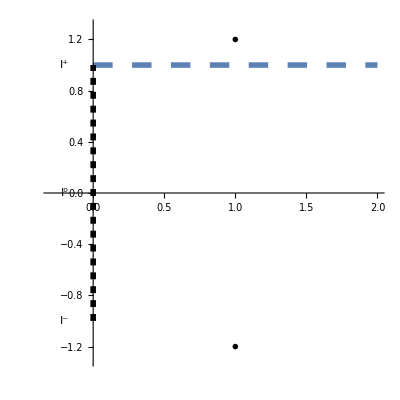

```mathematica
FutureNullInfinityFriedrichPlot=Plot[1,{rho,0,2},PlotRange->{{-0.3,2},{-1.3,1.3}},AspectRatio->1,PlotStyle->{Thickness[0.01],Dashing[Large]},Epilog->{{Directive[spinflineStyle],Line[{{0,-1},{0,1}}]},Text[MaTeX["\\scri^+",Magnification->2],{1,1.2}],Text[MaTeX["\\scri^-",Magnification->2],{1,-1.2}],Text[Style["I^+",Large],{-0.2,1}],Text[Style["I^-",Large],{-0.2,-1}],Text[Style["I^0",Large],{-0.2,0}]}]
```

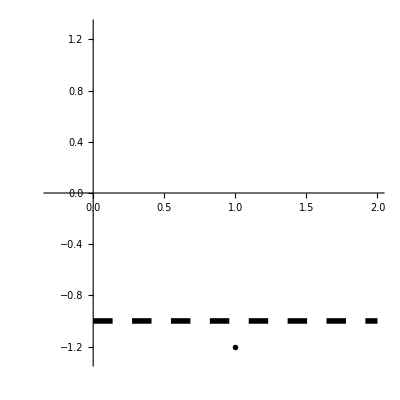

```mathematica
PastNullInfinityFriedrichPlot=Plot[-1,{rho,0,2},PlotRange->{{-0.3,2},{-1.3,1.3}},AspectRatio->1,PlotStyle->{Thickness[0.01],Dashing[Large],Black},Epilog->{Text[MaTeX["\\scri^-",Magnification->2],{1,-1.2}]}]
```

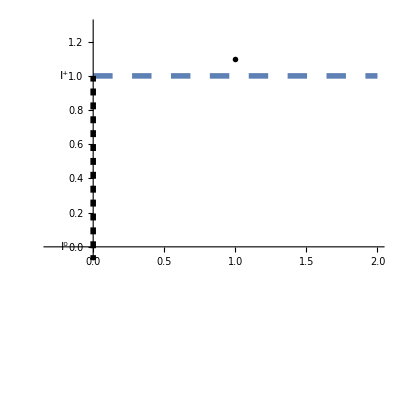

```mathematica
FutureNullInfinityFriedrichPlotHalf=Plot[1,{rho,0,2},PlotRange->{{-0.3,2},{-0.05,1.3}},AspectRatio->1,PlotStyle->{Thickness[0.01],Dashing[Large]},Epilog->{{Directive[spinflineStyle],Line[{{0,-1},{0,1}}]},Text[MaTeX["\\scri^+",Magnification->2],{1,1.1}],Text[Style["I^+",Large],{-0.2,1}],Text[Style["I^-",Large],{-0.2,-1}],Text[Style["I^0",Large],{-0.2,0}]}]
```

```mathematica
CauchySurfacesInFriedrich[tphys_]:=Evaluate[{FtoPhys[[1,2]],FtoPhys[[2,2]]}]
```

```mathematica
RelativisticPlotToMathematicaPlotOrder[CauchySurfacesInFriedrich[0]]
```

{1/(r̃),0}

```mathematica
ListOfCauchySlicesInFriedrich={RelativisticPlotToMathematicaPlotOrder[CauchySurfacesInFriedrich[0]],RelativisticPlotToMathematicaPlotOrder[CauchySurfacesInFriedrich[0.1]],RelativisticPlotToMathematicaPlotOrder[CauchySurfacesInFriedrich[0.5]],RelativisticPlotToMathematicaPlotOrder[CauchySurfacesInFriedrich[1.5]]};
```

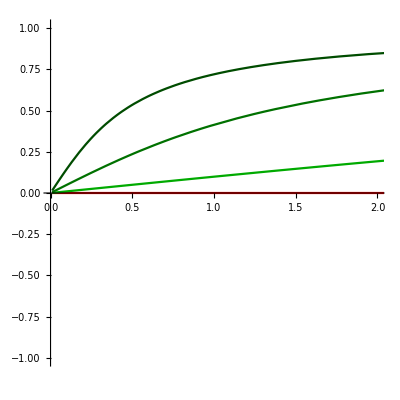

```mathematica
CauchySurfacesPenrosePlotFriedrich=ParametricPlot[ListOfCauchySlicesInFriedrich,{rphys,0,100},PlotRange->{{0,2},{-1.01,1.01}},AspectRatio->1,PlotStyle->{Red,Darker[Green],Darker[Darker[Green]],Darker[Darker[Darker[Green]]]}]
```

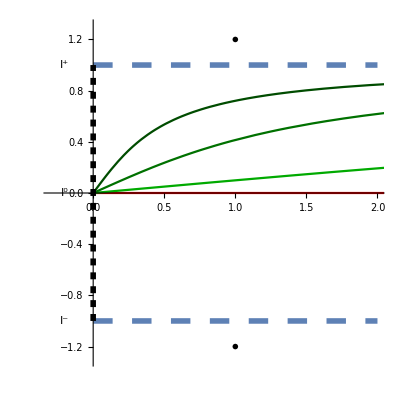

```mathematica
Show[FutureNullInfinityFriedrichPlot,CauchySurfacesPenrosePlotFriedrich,PastNullInfinityFriedrichPlot]
```

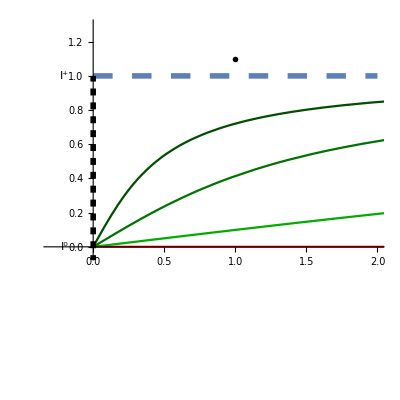

```mathematica
Show[FutureNullInfinityFriedrichPlotHalf,CauchySurfacesPenrosePlotFriedrich,PastNullInfinityFriedrichPlot]
```

Hyperboloidal  to Physical

```mathematica
GeneralHyptoRelation={thyp==tphys-height[rphys],rphys==rhyp/Omega[rhyp]}
```

{t==t̃-h[r̃],r̃==r/Ω[r]}

```mathematica
AnnilsHeight=height[x_]:>Sqrt[a^2+x^2]
AnnilsOmega=Omega[x_]:>1-x
```

h[x_]:>√(a^2+x^2)

Ω[x_]:>1-x

```mathematica
GeneralHyptoRelation
%/.AnnilsHeight/.AnnilsOmega
Flatten@(Solve[%,{thyp,rhyp}]/.Rule->Equal);
AnnilHyptoPhys=%
```

{t==t̃-h[r̃],r̃==r/Ω[r]}

{t==-√(a^2+(r̃)^2)+t̃,r̃==r/(1-r)}

{t==-√(a^2+(r̃)^2)+t̃,r==(r̃)/(1+r̃)}

```mathematica
AnnilPhysToHyp=(Flatten@Solve[AnnilHyptoPhys,{tphys,rphys}]/.Rule->Equal)
```

{t̃==√(a^2+r^2/(-1+r)^2)+t,r̃==-r/(-1+r)}

#### Hyperboloidal slices in Penrose Diagram

```mathematica
trpenTophys
%/.(AnnilPhysToHyp/.Equal->Rule);
PenToHyp=%
```

{T==ArcTan[(2 t̃)/(1+(r̃)^2-(t̃)^2)],ψ==ArcTan[(2 r̃)/(1-(r̃)^2+(t̃)^2)]}

{T==ArcTan[(2 (√(a^2+r^2/(-1+r)^2)+t))/(1+r^2/(-1+r)^2-(√(a^2+r^2/(-1+r)^2)+t)^2)],ψ==-ArcTan[(2 r)/((-1+r) (1-r^2/(-1+r)^2+(√(a^2+r^2/(-1+r)^2)+t)^2))]}

Check future null infinity location

```mathematica
tpen+rpen
%/.(PenToHyp/.Equal->Rule)
%/.a->2;
Limit[%,rhyp->1,Direction->"FromBelow"]
```

ψ+T

ArcTan[(2 (√(a^2+r^2/(-1+r)^2)+t))/(1+r^2/(-1+r)^2-(√(a^2+r^2/(-1+r)^2)+t)^2)]-ArcTan[(2 r)/((-1+r) (1-r^2/(-1+r)^2+(√(a^2+r^2/(-1+r)^2)+t)^2))]

0

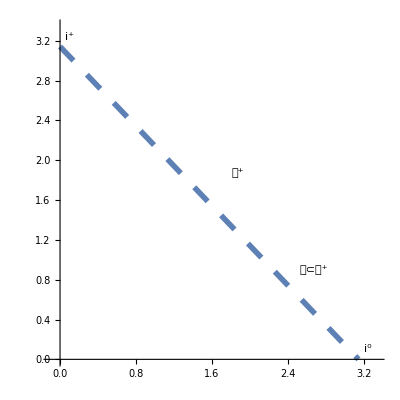

```mathematica
FutureNullInfinityPlotNew=Plot[Pi-rpen,{rpen,0,Pi},PlotRange->{{-0.1,Pi+0.2},{0,Pi+0.2}},AspectRatio->1,PlotStyle->{Thickness[0.01],Dashing[Large]},Epilog->{Text[Style["𝒥^+",Large],{Pi/2+0.3,Pi/2+0.3}],Text[Style["i^0",Large],{Pi+0.1,0.1}],Text[Style["i^+",Large],{0.1,Pi+0.1}],Text[Style["𝒞⊂𝒥^+",Large],{Pi/2+1.1,0.9}]}]
```

```mathematica
HyperboloidalSurfacesInPenrose[thyp_]:=Evaluate[{PenToHyp[[1,2]],PenToHyp[[2,2]]}]
```

```mathematica
ListOfHyperboloidalSurfacesInPenrose={RelativisticPlotToMathematicaPlotOrder[HyperboloidalSurfacesInPenrose[0]],RelativisticPlotToMathematicaPlotOrder[HyperboloidalSurfacesInPenrose[0.5]],RelativisticPlotToMathematicaPlotOrder[HyperboloidalSurfacesInPenrose[1.3]],RelativisticPlotToMathematicaPlotOrder[HyperboloidalSurfacesInPenrose[3]]}/.{a->1};
```

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0. encountered.

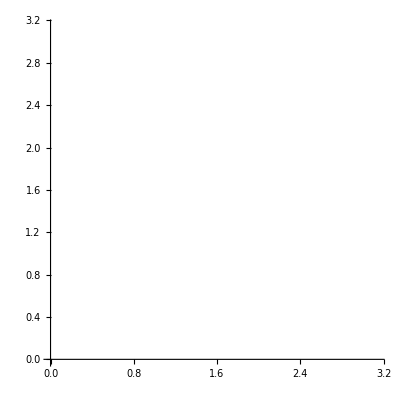

```mathematica
HyperboloidalSurfacesPenrosePlot=ParametricPlot[ListOfHyperboloidalSurfacesInPenrose,{rhyp,0,1},PlotRange->{{0,Pi},{0,Pi}},AspectRatio->1,PlotStyle->{Red,Darker[Green],Darker[Darker[Green]],Darker[Darker[Darker[Green]]]}]
```

```mathematica
Show[FutureNullInfinityPlotNew,HyperboloidalSurfacesPenrosePlot]
```

-Graphics-

```mathematica
ListOfHyperboloidalNegativeTimesSurfacesInPenrose={RelativisticPlotToMathematicaPlotOrder[HyperboloidalSurfacesInPenrose[0]],RelativisticPlotToMathematicaPlotOrder[HyperboloidalSurfacesInPenrose[-0.45]],RelativisticPlotToMathematicaPlotOrder[HyperboloidalSurfacesInPenrose[-0.9]],RelativisticPlotToMathematicaPlotOrder[HyperboloidalSurfacesInPenrose[-1.7]],RelativisticPlotToMathematicaPlotOrder[HyperboloidalSurfacesInPenrose[-5]]}/.{a->1};
```

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0. encountered.

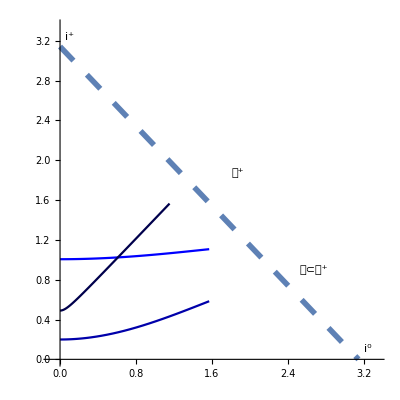

```mathematica
HyperboloidalSurfacesNegativePenrosePlot=ParametricPlot[ListOfHyperboloidalNegativeTimesSurfacesInPenrose,{rhyp,0,1},PlotRange->{{0,Pi},{0,Pi}},AspectRatio->1,PlotStyle->{Red,Blue,Darker[Blue],Darker[Darker[Blue]],Darker[Darker[Darker[Blue]]]}];
Show[FutureNullInfinityPlotNew,HyperboloidalSurfacesNegativePenrosePlot]
```

```mathematica
Show[FutureNullInfinityPlotNew,HyperboloidalSurfacesPenrosePlot,HyperboloidalSurfacesNegativePenrosePlot]
```

-Graphics-

#### Friedrich to Hyperboloidal (with Annil’s choice of Height and Compression functions)

```mathematica
FtoPhys;
%/.(AnnilPhysToHyp/.Equal->Rule);
FtoHyp=%
(*%//Together//PowerExpand*)
```

{τ==-((-1+r) (√(a^2+r^2/(-1+r)^2)+t))/r,ρ==-r/((-1+r) (r^2/(-1+r)^2-(√(a^2+r^2/(-1+r)^2)+t)^2))}

```mathematica
AnnilHyptoPhys
%/.(PhysToF/.Equal->Rule);
HypToF=%
```

{t==-√(a^2+(r̃)^2)+t̃,r==(r̃)/(1+r̃)}

{t==-τ/(ρ (-1+τ^2))-√(a^2+1/(ρ^2 (-1+τ^2)^2)),r==-1/(ρ (-1+τ^2) (1-1/(ρ (-1+τ^2))))}

```mathematica
FtoHyp
(*%/.rhyp->1*)
```

{τ==-((-1+r) (√(a^2+r^2/(-1+r)^2)+t))/r,ρ==-r/((-1+r) (r^2/(-1+r)^2-(√(a^2+r^2/(-1+r)^2)+t)^2))}

#### Plot of hyperboloidal slices on Friedrich diagram

```mathematica
HyperboloidalSurfacesInFriedrich[thyp_]:=Evaluate[{FtoHyp[[1,2]],FtoHyp[[2,2]]}]
```

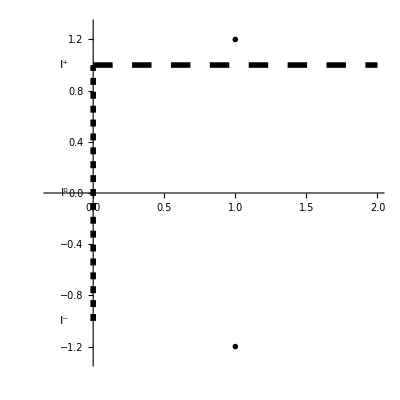

```mathematica
FutureNullInfinityFriedrichPlotNew=Plot[1,{rho,0,2},PlotRange->{{-0.3,2},{-1.3,1.3}},AspectRatio->1,PlotStyle->{Thickness[0.01],Dashing[Large],Black},Epilog->{{Directive[spinflineStyle],Line[{{0,-1},{0,1}}]},Text[MaTeX["\\scri^+",Magnification->2],{1,1.2}],Text[MaTeX["\\scri^-",Magnification->2],{1,-1.2}],Text[Style["I^+",Large],{-0.2,1}],Text[Style["I^-",Large],{-0.2,-1}],Text[Style["I^0",Large],{-0.2,0}]}]
```

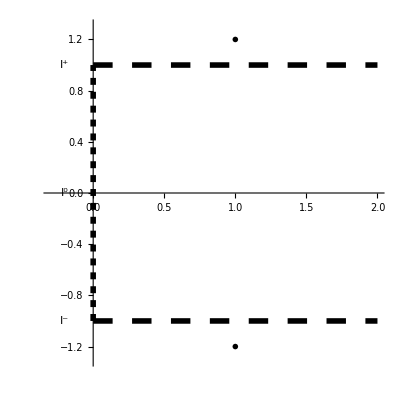

```mathematica
Show[FutureNullInfinityFriedrichPlotNew,PastNullInfinityFriedrichPlot]
```

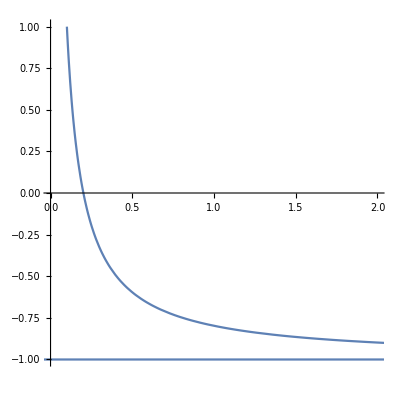

```mathematica
ParametricPlot[RelativisticPlotToMathematicaPlotOrder[HyperboloidalSurfacesInFriedrich[-5]/.a->1/2],{rhyp,0,1},AspectRatio->1,PlotRange->{{0,2},{-1,1}}]
```

```mathematica
(*ListOfHyperboloidalNegativeTimesSurfacesInFriedrich={RelativisticPlotToMathematicaPlotOrder[HyperboloidalSurfacesInFriedrich[0]],RelativisticPlotToMathematicaPlotOrder[HyperboloidalSurfacesInFriedrich[-1]],RelativisticPlotToMathematicaPlotOrder[HyperboloidalSurfacesInFriedrich[-2]],RelativisticPlotToMathematicaPlotOrder[HyperboloidalSurfacesInFriedrich[-5]]}/.{a->1/2};*)
```

```mathematica
ListOfHyperboloidalNegativeTimesSurfacesInFriedrich={RelativisticPlotToMathematicaPlotOrder[HyperboloidalSurfacesInFriedrich[0]],RelativisticPlotToMathematicaPlotOrder[HyperboloidalSurfacesInFriedrich[-0.9]],RelativisticPlotToMathematicaPlotOrder[HyperboloidalSurfacesInFriedrich[-1.7]],RelativisticPlotToMathematicaPlotOrder[HyperboloidalSurfacesInFriedrich[-5]]}/.{a->1/2};
```

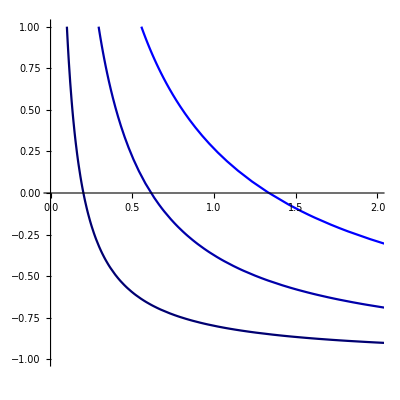

```mathematica
HyperboloidalSurfacesNegativeTimesFriedrichPlot=ParametricPlot[ListOfHyperboloidalNegativeTimesSurfacesInFriedrich,{rhyp,0,1},AspectRatio->1,PlotRange->{{0,2},{-1,1}},PlotStyle->{Red,Blue,Darker[Blue],Darker[Darker[Blue]]}]
```

```mathematica
(*HyperboloidalSurfacesNegativeTimesFriedrichPlot=ParametricPlot[ListOfHyperboloidalNegativeTimesSurfacesInFriedrich,{rhyp,0,1},AspectRatio->1,(*PlotRange->{{0,2},{-1,1}},*)PlotStyle->{Red,Blue,Darker[Blue],Darker[Darker[Blue]]}]*)
```

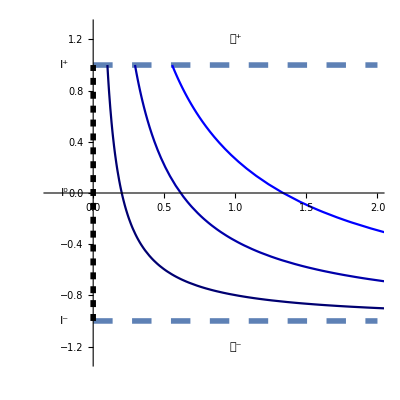

```mathematica
Show[FutureNullInfinityFriedrichPlotNew,PastNullInfinityFriedrichPlot,HyperboloidalSurfacesNegativeTimesFriedrichPlot]
```

## Partial waves

### Waves on Cauchy slices

```mathematica
(*Plot[2 Sin[x],{x,0,10},,LabelStyle->Directive[Blue,Bold]]*)
```

```mathematica
PartialWaveu[k_,omega_,tphys_,rphys_]:=Exp[2*Pi*I*(k*rphys-omega*tphys)]
```

```mathematica
PartialWaveu[k,ω,tphys,rphys]
%//ExpToTrig
Refine[Re[%],{rphys>0,tphys>0}]
```

ⅇ^(2 ⅈ π (k r̃-t̃ ω))

Cos[2 k π r̃-2 π t̃ ω]+ⅈ Sin[2 k π r̃-2 π t̃ ω]

-Im[Sin[2 k π r̃-2 π t̃ ω]]+Re[Cos[2 k π r̃-2 π t̃ ω]]

#### Wave at Cauchy hypersurface t̃=0 with finite range in radius range 0<= r̃ <=3

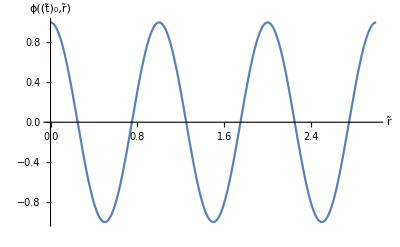

```mathematica
Plot[Re[PartialWaveu[1,1,0,rphys]],{rphys,0,3},AxesLabel->{"r̃","ϕ((t̃)_0,r̃)"} (*AxesLabel->{Style[r̃,Large] ,Style[ϕ,Large]}*)]
```

Wave at Cauchy hypersurface with compactified raidus only --i.e. not hyperboloidal!

We grab only the radial compactification . So that the coordinates are ( t̃ ,r )  -- physical time and compactified radius

```mathematica
AnnilPhysToHyp[[2]]
```

r̃==-r/(-1+r)

```mathematica
PartialWaveu[k,ω,tphys,rphys]
%/.(AnnilPhysToHyp[[2]]/.Equal->Rule)
PartialWaveuCompactifiedForm=%
```

ⅇ^(2 ⅈ π (k r̃-t̃ ω))

ⅇ^(2 ⅈ π (-(k r)/(-1+r)-t̃ ω))

ⅇ^(2 ⅈ π (-(k r)/(-1+r)-t̃ ω))

```mathematica
PartialWaveuCompactifiedForm[[2]]
Together[Simplify[%]]
%//Simplify
```

2 ⅈ π (-(k r)/(-1+r)-t̃ ω)

-(2 ⅈ π (k r-t̃ ω+r t̃ ω))/(-1+r)

-(2 ⅈ π (k r+(-1+r) t̃ ω))/(-1+r)

```mathematica
PlotRange->{{0,1.2},{-1,1}},Epilog->{Text[Style["𝒥^+",Large],{1.1,0}]}
```

```mathematica
PartialWaveuCompactifiedRadiusu[k_,ω_,tphys_,rhyp_]:=E^((2*I)*Pi*(-((k*rhyp)/(-1 + rhyp)) - tphys*ω))
```

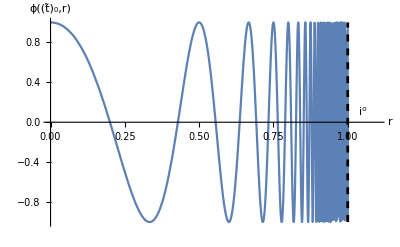

```mathematica
Plot[Re[PartialWaveuCompactifiedRadiusu[1,1,0,rhyp]],{rhyp,0,1},AxesLabel->{"r","ϕ((t̃)_0,r)"} ,PlotRange->{{0,1.1},{-1,1}},Epilog->{Text[Style["i^0",Large],{1.05,0.1}],Directive[LineSlimStyle],Line[{{1,-1},{1,1}}]}]
```

### Waves on hyperboloids

Wave at hyperboloidal surface

Hyperboloidal : Substitute both hyperboloidal time and compactified radius .

Notice that in Zen10 Annil gives two different examples of Height function.
This is the other height function he gives in Zen10.

```mathematica
AnnilsHeightOther=height[x_]:>(x+c/(1+x))
AnnilsOmegaOther=Omega[x_]:>1-x
```

h[x_]:>x+c/(1+x)

Ω[x_]:>1-x

```mathematica
GeneralHyptoRelation
%/.AnnilsHeightOther/.AnnilsOmegaOther
Flatten@(Solve[%,{thyp,rhyp}]/.Rule->Equal);
AnnilHyptoPhysOther=%
```

{t==t̃-h[r̃],r̃==r/Ω[r]}

{t==-r̃-c/(1+r̃)+t̃,r̃==r/(1-r)}

{t==(-c-r̃-(r̃)^2+t̃+r̃ t̃)/(1+r̃),r==(r̃)/(1+r̃)}

```mathematica
AnnilPhysToHypOther=(Flatten@Solve[AnnilHyptoPhysOther,{tphys,rphys}]//Simplify/.Rule->Equal)
```

{t̃→-(c (-1+r)^2+r+t-r t)/(-1+r),r̃→-r/(-1+r)}

```mathematica
AnnilPhysToHypOther
```

{t̃→-(c (-1+r)^2+r+t-r t)/(-1+r),r̃→-r/(-1+r)}

```mathematica
PartialWaveu[k,ω,tphys,rphys]
%/.(AnnilPhysToHypOther/.Equal->Rule)
%//Expand//Simplify;
PartialWaveuHyperboloidalForm=%
```

ⅇ^(2 ⅈ π (k r̃-t̃ ω))

ⅇ^(2 ⅈ π (-(k r)/(-1+r)+((c (-1+r)^2+r+t-r t) ω)/(-1+r)))

ⅇ^((2 ⅈ π (-k r+(c (-1+r)^2+r+t-r t) ω))/(-1+r))

```mathematica
(-(k*rhyp) + (c*(-1 + rhyp)^2 + rhyp + thyp - rhyp*thyp)*ω)/(-1 + rhyp)
%/.{k->1,ω->1}
%//FullSimplify
```

(-k r+(c (-1+r)^2+r+t-r t) ω)/(-1+r)

(c (-1+r)^2+t-r t)/(-1+r)

c (-1+r)-t

```mathematica
PartialWaveHyperboloidal[c_,k_,ω_,thyp_,rhyp_]:=E^(((2*I)*Pi*(-(k*rhyp)+(c*(-1+rhyp)^2+rhyp+thyp-rhyp*thyp)*ω))/(-1+rhyp))
```

```mathematica
PartialWaveHyperboloidal[1,1,1,thyp,rhyp]//FullSimplify
```

ⅇ^(2 ⅈ π (-1+r-t))

#### Plots using Annil' s second hyperboloidal foliation

#### Wave on hyperboloidal slice t = 0 with k = ω

```mathematica
LineSlimStyle={Thickness[0.005],Black,Dashed};
```

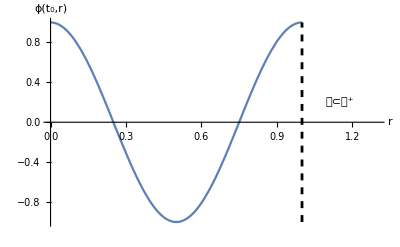

```mathematica
Plot[Re[PartialWaveHyperboloidal[1,1,1,0,rhyp]//FullSimplify],{rhyp,0,1},AxesLabel->{"r","ϕ(t_0,r)"} ,PlotRange->{{0,1.3},{-1,1}},Epilog->{Text[Style["𝒞⊂𝒥^+",Large],{1.15,0.2}],{Directive[LineSlimStyle],Line[{{1,-1},{1,1}}]}}]
```

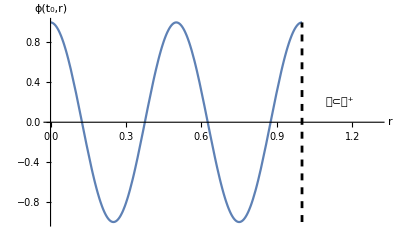

```mathematica
Plot[Re[PartialWaveHyperboloidal[1,2,2,0,rhyp]//FullSimplify],{rhyp,0,1},AxesLabel->{"r","ϕ(t_0,r)"},PlotRange->{{0,1.3},{-1,1}},Epilog->{Text[Style["𝒞⊂𝒥^+",Large],{1.15,0.2}],{Directive[LineSlimStyle],Line[{{1,-1},{1,1}}]}}]
```

#### Wave on hyperboloidal slice t = 0 with k different from ω

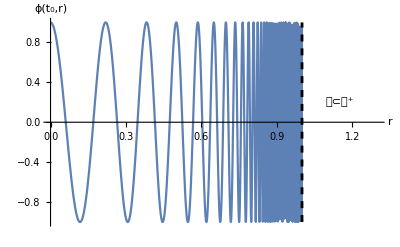

```mathematica
Plot[Re[PartialWaveHyperboloidal[2,3,1,3,rhyp]//FullSimplify],{rhyp,0,1},AxesLabel->{"r","ϕ(t_0,r)"},PlotRange->{{0,1.3},{-1,1}},Epilog->{Text[Style["𝒞⊂𝒥^+",Large],{1.15,0.2}],{Directive[LineSlimStyle],Line[{{1,-1},{1,1}}]}}]
```

Note : Annil does not comment about this "fine tuned" behaviour or that thing only work if one chooses k = ω

Understanding the reason for this fine tuned behaviour

```mathematica
PartialWaveHyperboloidal[c,k,ω,thyp,rhyp]
%[[2]]
Limit[%,rhyp->1]
```

ⅇ^((2 ⅈ π (-k r+(c (-1+r)^2+r+t-r t) ω))/(-1+r))

(2 ⅈ π (-k r+(c (-1+r)^2+r+t-r t) ω))/(-1+r)

Indeterminate

```mathematica
PartialWaveHyperboloidal[c,ω,ω,thyp,rhyp]
%[[2]]
Limit[%,rhyp->1]
```

ⅇ^((2 ⅈ π (-r ω+(c (-1+r)^2+r+t-r t) ω))/(-1+r))

(2 ⅈ π (-r ω+(c (-1+r)^2+r+t-r t) ω))/(-1+r)

-2 ⅈ π t ω

### Waves on the standard hyperboloidal foliation

The standard hyperboloidal foliation gives

```mathematica
PartialWaveu[k,ω,tphys,rphys]
%/.(AnnilPhysToHyp/.Equal->Rule)
%//Expand//Simplify;
PartialWaveuHyperboloidalFormStandardHyp=%
```

ⅇ^(2 ⅈ π (k r̃-t̃ ω))

ⅇ^(2 ⅈ π (-(k r)/(-1+r)-(√(a^2+r^2/(-1+r)^2)+t) ω))

ⅇ^(2 ⅈ π (-(k r)/(-1+r)-(√(a^2+r^2/(-1+r)^2)+t) ω))

```mathematica
InputForm[PartialWaveuHyperboloidalFormStandardHyp]
```

E^((2*I)*Pi*(-((k*rhyp)/(-1 + rhyp)) - (Sqrt[a^2 + rhyp^2/(-1 + rhyp)^2] + thyp)*ω))

```mathematica
PartialWaveHyperboloidalStandardHyp[a_,k_,ω_,thyp_,rhyp_]:=E^((2*I)*Pi*(-((k*rhyp)/(-1+rhyp))-(Sqrt[a^2+rhyp^2/(-1+rhyp)^2]+thyp)*ω))
```

Wave on hyperboloidal slice t = 0 with k = ω

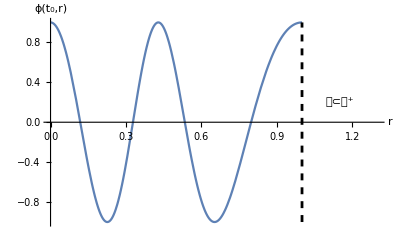

```mathematica
Plot[Re[PartialWaveHyperboloidalStandardHyp[1,2,2,0,rhyp]//FullSimplify],{rhyp,0,1},AxesLabel->{"r","ϕ(t_0,r)"} ,PlotRange->{{0,1.3},{-1,1}},Epilog->{Text[Style["𝒞⊂𝒥^+",Large],{1.15,0.2}],{Directive[LineSlimStyle],Line[{{1,-1},{1,1}}]}}]
```

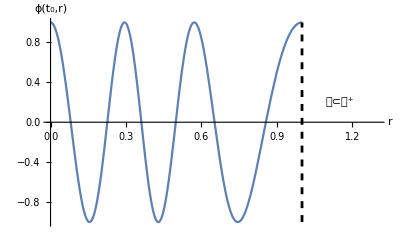

```mathematica
Plot[Re[PartialWaveHyperboloidalStandardHyp[1,3,3,0,rhyp]//FullSimplify],{rhyp,0,1},AxesLabel->{"r","ϕ(t_0,r)"},PlotRange->{{0,1.3},{-1,1}},Epilog->{Text[Style["𝒞⊂𝒥^+",Large],{1.15,0.2}],{Directive[LineSlimStyle],Line[{{1,-1},{1,1}}]}} ]
```

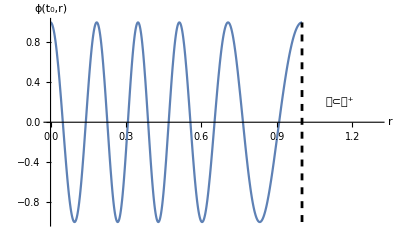

```mathematica
Plot[Re[PartialWaveHyperboloidalStandardHyp[1,5,5,0,rhyp]//FullSimplify],{rhyp,0,1},AxesLabel->{"r","ϕ(t_0,r)"},PlotRange->{{0,1.3},{-1,1}},Epilog->{Text[Style["𝒞⊂𝒥^+",Large],{1.15,0.2}],{Directive[LineSlimStyle],Line[{{1,-1},{1,1}}]}} ]
```

Wave on hyperboloidal slice t = 0 with k different from ω

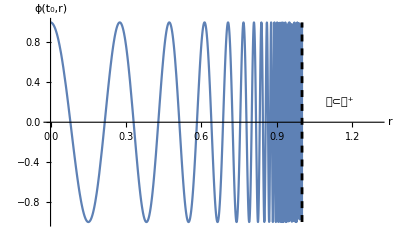

```mathematica
Plot[Re[PartialWaveHyperboloidalStandardHyp[1,3,2,0,rhyp]//FullSimplify],{rhyp,0,1},AxesLabel->{"r","ϕ(t_0,r)"} ,PlotRange->{{0,1.3},{-1,1}},Epilog->{Text[Style["𝒞⊂𝒥^+",Large],{1.15,0.2}],{Directive[LineSlimStyle],Line[{{1,-1},{1,1}}]}}]
```

Note : Annil does not comment about this "fine tuned" behaviour or that thing only work if one chooses k = ω

Understanding this fine tuned behaviour

```mathematica
PartialWaveHyperboloidalStandardHyp[1,k,ω,thyp,rhyp]
%//ExpToTrig
Refine[Re[%],{0<rhyp<1,k>0,ω>0,thyp>0}]
```

ⅇ^(2 ⅈ π (-(k r)/(-1+r)-(√(1+r^2/(-1+r)^2)+t) ω))

Cos[(2 k π r)/(-1+r)+2 π √(1+r^2/(-1+r)^2) ω+2 π t ω]-ⅈ Sin[(2 k π r)/(-1+r)+2 π √(1+r^2/(-1+r)^2) ω+2 π t ω]

Cos[(2 k π r)/(-1+r)+2 π √(1+r^2/(-1+r)^2) ω+2 π t ω]

```mathematica
PartialWaveHyperboloidalStandardHyp[1,k,ω,thyp,rhyp];
%//ExpToTrig;
Refine[Re[%],{0<rhyp<1,k>0,ω>0,thyp>0}];
%[[1]]
Limit[%,rhyp->1,Direction->"FromBelow"]
```

(2 k π r)/(-1+r)+2 π √(1+r^2/(-1+r)^2) ω+2 π t ω

(-k+ω) ∞

```mathematica
SimplyfySqrt=Sqrt[x_]:>Sqrt[Together[x]]
```

√x_:>√Together[x]

```mathematica
PartialWaveHyperboloidalStandardHyp[1,k,ω,t,rhyp]
%[[2,-1]]
%//Together//PowerExpand;
%//Simplify
(*%/.SimplyfySqrt*)
Simplify[%,Assumptions->rhyp<1]
(*%/.{k->ω}*)
Limit[%,rhyp->1]
```

ⅇ^(2 ⅈ π (-(k r)/(-1+r)-(√(1+r^2/(-1+r)^2)+t) ω))

-(k r)/(-1+r)-(√(1+r^2/(-1+r)^2)+t) ω

-(k r)/(-1+r)-(√((1-2 r+2 r^2)/(-1+r)^2)+t) ω

(-k r+(√(1-2 r+2 r^2)+t-r t) ω)/(-1+r)

Indeterminate

```mathematica
PartialWaveHyperboloidalStandardHyp[1,k,ω,t,rhyp]
%[[2,-1]]
%//Together//PowerExpand;
%//Simplify
(*%/.SimplyfySqrt*)
Simplify[%,Assumptions->rhyp<1]
%/.{k->ω}
Limit[%,rhyp->1]
```

ⅇ^(2 ⅈ π (-(k r)/(-1+r)-(√(1+r^2/(-1+r)^2)+t) ω))

-(k r)/(-1+r)-(√(1+r^2/(-1+r)^2)+t) ω

-(k r)/(-1+r)-(√((1-2 r+2 r^2)/(-1+r)^2)+t) ω

(-k r+(√(1-2 r+2 r^2)+t-r t) ω)/(-1+r)

(-r ω+(√(1-2 r+2 r^2)+t-r t) ω)/(-1+r)

-t ω

```mathematica
PartialWaveHyperboloidalStandardHyp[1,k,k,0,rhyp];
%//ExpToTrig;
Refine[Re[%],{0<rhyp<1,k>0,ω>0,thyp>0}];
%[[1]]//FullSimplify
%//Together
Limit[%,rhyp->1,Direction->"FromBelow"]
```

2 k π (1+1/(-1+r)+√(1+r^2/(-1+r)^2))

(2 k π (r-√(1+r^2/(-1+r)^2)+r √(1+r^2/(-1+r)^2)))/(-1+r)

0

```mathematica
qttTilde/:MakeBoxes[qttTilde,StandardForm]:="OverTilde[q_tt]";
qtrTilde/:MakeBoxes[qtrTilde,StandardForm]:="OverTilde[q_tr]";
qrrTilde/:MakeBoxes[qrrTilde,StandardForm]:="OverTilde[q_rr]";
```

```mathematica
qtt/:MakeBoxes[qtt,StandardForm]:="q_tt";
qtr/:MakeBoxes[qtr,StandardForm]:="q_tr";
qrr/:MakeBoxes[qrr,StandardForm]:="q_rr";
```

```mathematica
{qtt==Omega[R]*qttTilde,qtr==qttTilde*height'[R](Omega[R]-Omega'[R]*rhyp),qrr==((qttTilde*(height'[R])^2+qrrTilde)/Omega[R]^2)(Omega[R]-Omega'[R]rhyp)^2}
```

{q_tt==OverTilde[q_tt] Ω[R],q_tr==OverTilde[q_tt] h'[R] (Ω[R]-r Ω'[R]),q_rr==((OverTilde[q_rr]+OverTilde[q_tt] h'[R]^2) (Ω[R]-r Ω'[R])^2)/Ω[R]^2}

## Waves on the cylinder at spatial infinity

```mathematica
PartialWaveu[k,ω,tphys,rphys]
%/.(PhysToF/.Equal->Rule)
%//FullSimplify;
PartialWaveCylinderForm=%
```

ⅇ^(2 ⅈ π (k r̃-t̃ ω))

ⅇ^(2 ⅈ π (-k/(ρ (-1+τ^2))+(τ ω)/(ρ (-1+τ^2))))

ⅇ^((2 ⅈ π (-k+τ ω))/(ρ (-1+τ^2)))

```mathematica
InputForm[PartialWaveCylinderForm]
```

E^(((2*I)*Pi*(-k + tau*ω))/(rho*(-1 + tau^2)))

```mathematica
PartialWaveuCylinder[k_,ω_,tau_,rho_]:=E^(((2*I)*Pi*(-k+tau*ω))/(rho*(-1+tau^2)))
```

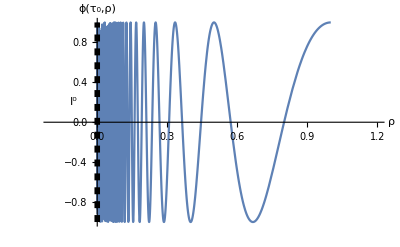

```mathematica
Plot[Re[PartialWaveuCylinder[1,1,0,rho]//FullSimplify],{rho,0,1},AxesLabel->{"ρ","ϕ(τ_0,ρ)"} ,PlotRange->{{-0.2,1.2},{-1,1}},Epilog->{Text[Style["I^0",Large],{-0.1,0.2}],{Directive[spinflineStyle],Line[{{0,-1},{0,1}}]}}]
```

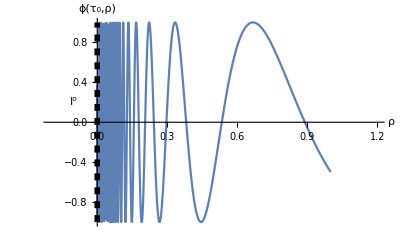

```mathematica
Plot[Re[PartialWaveuCylinder[1,1,0.5,rho]//FullSimplify],{rho,0,1},AxesLabel->{"ρ","ϕ(τ_0,ρ)"},PlotRange->{{-0.2,1.2},{-1,1}},Epilog->{Text[Style["I^0",Large],{-0.1,0.2}],{Directive[spinflineStyle],Line[{{0,-1},{0,1}}]}}]
```

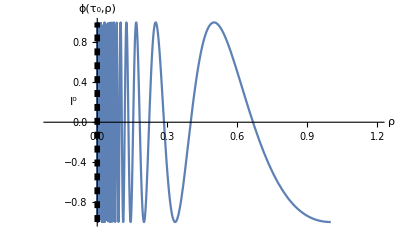

```mathematica
Plot[Re[PartialWaveuCylinder[1,1,0.999,rho]//FullSimplify],{rho,0,1},AxesLabel->{"ρ","ϕ(τ_0,ρ)"},PlotRange->{{-0.2,1.2},{-1,1}},Epilog->{Text[Style["I^0",Large],{-0.1,0.2}],{Directive[spinflineStyle],Line[{{0,-1},{0,1}}]}}]
```

So at the critical set something goes wrong if the limit is taken without fine tuning k and ω

```mathematica
Plot[Re[PartialWaveuCylinder[1,1,1,rho]//FullSimplify],{rho,0,1},AxesLabel->{"ρ","ϕ(τ_0,ρ)"}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

For fined tuned values of k, ω and τ we can approach the τ=1 limit as follows.

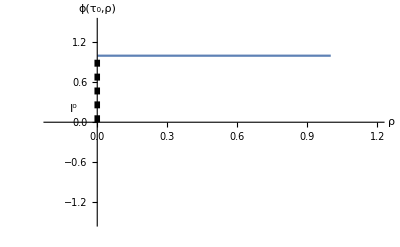

```mathematica
Plot[Re[PartialWaveuCylinder[2,3,2/3,rho]//FullSimplify],{rho,0,1},AxesLabel->{"ρ","ϕ(τ_0,ρ)"},PlotRange->{{-0.2,1.2},{-1.5,1.5}},Epilog->{Text[Style["I^0",Large],{-0.1,0.2}],{Directive[spinflineStyle],Line[{{0,0},{0,1}}]}}]
```

```mathematica
Plot[Re[PartialWaveuCylinder[4,5,4/5,rho]//FullSimplify],{rho,0,1},AxesLabel->{"ρ","ϕ(τ_0,ρ)"},PlotRange->{{-0.2,1.2},{-1.5,1.5}},Epilog->{Text[Style["I^0",Large],{-0.1,0.2}],{Directive[spinflineStyle],Line[{{0,0},{0,1}}]}}]
```

-Graphics-

```mathematica
Plot[Re[PartialWaveuCylinder[5,6,5/6,rho]//FullSimplify],{rho,0,1},AxesLabel->{"ρ","ϕ(τ_0,ρ)"},PlotRange->{{-0.2,1.2},{-1.5,1.5}},Epilog->{Text[Style["I^0",Large],{-0.1,0.2}],{Directive[spinflineStyle],Line[{{0,0},{0,1}}]}}]
```

-Graphics-

Observe we are using the series {k=n, ω=n+1, t =n/(1+n)} which converges to {k=1, ω=1, t =1}

```mathematica
Limit[n/(n + 1),n->Infinity]
```

1

Understanding this fine tuned behaviour

```mathematica
(*Plot[Re[PartialWaveuCylinder[1,1,1,rho]//FullSimplify],{rho,0,1}]*)
```

```mathematica
PartialWaveuCylinder[k,ω,tau,rho]
%//ExpToTrig;
Refine[Re[%],{-1<tau<1,k>0,ω>0,rho>0}];
%[[1]]//FullSimplify;
ArgumentExpInCylinderForm=%
```

ⅇ^((2 ⅈ π (-k+τ ω))/(ρ (-1+τ^2)))

(2 π (k-τ ω))/(ρ-ρ τ^2)

```mathematica
PartialWaveuCylinder[k,k,tau,rho]
%//ExpToTrig;
Refine[Re[%],{-1<tau<1,k>0,ω>0,rho>0}];
%[[1]]//FullSimplify
```

ⅇ^((2 ⅈ π (-k+k τ))/(ρ (-1+τ^2)))

(2 k π)/(ρ+ρ τ)

```mathematica
PartialWaveuCylinder[k,-k,tau,rho]
%//ExpToTrig;
Refine[Re[%],{-1<tau<1,k>0,ω>0,rho>0}];
%[[1]]//FullSimplify
```

ⅇ^((2 ⅈ π (-k-k τ))/(ρ (-1+τ^2)))

(2 k π)/(ρ-ρ τ)

```mathematica
PartialWaveuCylinder[k,ω,k/ω,rho]
%//ExpToTrig
```

1

1

```mathematica
PartialWaveuCylinder[k,ω,tau,rho]
%//ExpToTrig;
Refine[Re[%],{-1<tau<1,k>0,ω>0,rho>0}];
%[[1]]//FullSimplify
Limit[%,{tau->k/ω}]
```

ⅇ^((2 ⅈ π (-k+τ ω))/(ρ (-1+τ^2)))

(2 π (k-τ ω))/(ρ-ρ τ^2)

0

So if we approach the τ = 1 hypersuface changing via the series tau = (k/ω) + ϵ and Taylor expand around ϵ = 0

```mathematica
PartialWaveuCylinder[k,ω,tau,rho]
%/.{rho->k-ω}
%/.{k->α,ω->α+1}
%/.{tau->α/(α+1)}
```

ⅇ^((2 ⅈ π (-k+τ ω))/(ρ (-1+τ^2)))

ⅇ^((2 ⅈ π (-k+τ ω))/((-1+τ^2) (k-ω)))

ⅇ^(-(2 ⅈ π (-α+τ (1+α)))/(-1+τ^2))

1

```mathematica
PartialWaveuCylinder[k,ω,tau,rho]
%/.{k->α,ω->α+1}
%/.{tau->α/(α+1)+ϵ}
%//FullSimplify;
PartialWaveuCylinderLimitingProcessForm=%
```

ⅇ^((2 ⅈ π (-k+τ ω))/(ρ (-1+τ^2)))

ⅇ^((2 ⅈ π (-α+τ (1+α)))/(ρ (-1+τ^2)))

ⅇ^((2 ⅈ π (-α+(1+α) (α/(1+α)+ϵ)))/(ρ (-1+(α/(1+α)+ϵ)^2)))

ⅇ^((2 ⅈ π (1+α)^3 ϵ)/(ρ (-1+ϵ+α ϵ) (1+ϵ+α (2+ϵ))))

```mathematica
PartialWaveuCylinderLimitingProcessForm
Series[%,{ϵ,0,1}]
PartialWaveuCylinderTaylorExpanded=Normal[%]
```

ⅇ^((2 ⅈ π (1+α)^3 ϵ)/(ρ (-1+ϵ+α ϵ) (1+ϵ+α (2+ϵ))))

1-(2 ⅈ π (1+α)^3 ϵ)/(ρ (1+2 α))+O[ϵ]^2

1-(2 ⅈ π (1+α)^3 ϵ)/(ρ (1+2 α))

So as long as k is different from ω taking the limit at the critical set exists if we approach it through constant τ hypersurfaces of the form tau = (k/ω)+ϵ

### QNMs travelling wave

Physical picture

```mathematica
PartialWaveu[k,ω,tphys,rphys]
%/.{k->ω}
%/.{ω->ωR+I*ωI}
%//Simplify
InputForm[%]
```

ⅇ^(2 ⅈ π (k r̃-t̃ ω))

ⅇ^(2 ⅈ π (r̃ ω-t̃ ω))

ⅇ^(2 ⅈ π (r̃ (ⅈ ωI+ωR)-t̃ (ⅈ ωI+ωR)))

ⅇ^(-2 π (r̃-t̃) (ωI-ⅈ ωR))

E^(-2*Pi*(rphys - tphys)*(ωI - I*ωR))

```mathematica
E^(-2*Pi*(rphys - tphys)*(ωI - I*ωR))
```

ⅇ^(-2 π (r̃-t̃) (ωI-ⅈ ωR))

```mathematica
PartialWaveuqnm[ωR_,ωI_,tphys_,rphys_]:=E^(-2*Pi*(rphys - tphys)*(ωI - I*ωR))
```

```mathematica
(*Plot[Re[PartialWaveuqnm[10,-0.5,tphys,2]//FullSimplify],{tphys,2,5},PlotRange->{{2,5},{-2,2}}]*)
```

The QNM - like model  is when k = ω with ω complex .

{ω -> ω_R + I*ω_Im}

The sign of ω_Im is chose so that one has decay in physical time .

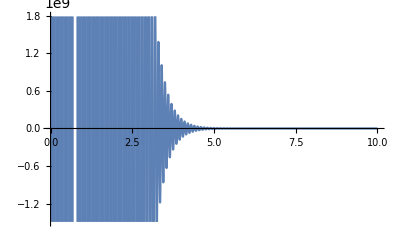

```mathematica
Plot[Re[PartialWaveu[10-0.5I,10-0.5I,tphys,10]],{tphys,0,10}]
```

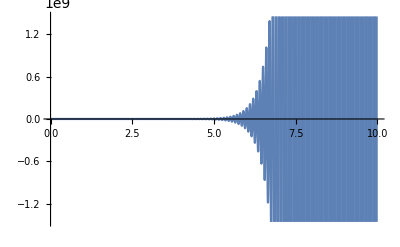

```mathematica
Plot[Re[PartialWaveuqnm[10,-0.5,0,rphys]//FullSimplify],{rphys,0,10}]
```

Hyperboloidal picture

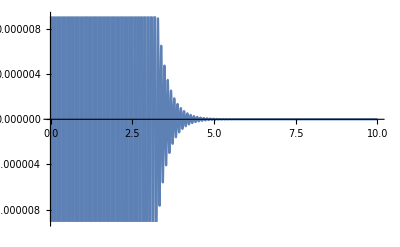

```mathematica
Plot[Re[PartialWaveHyperboloidalStandardHyp[1,10-0.5I,10-0.5I,thyp,0.5]//FullSimplify],{thyp,0,10}]
```

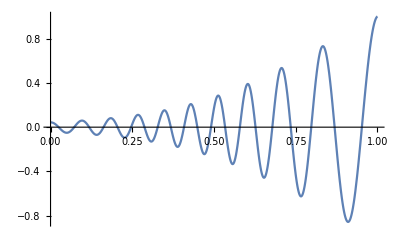

```mathematica
Plot[Re[PartialWaveHyperboloidalStandardHyp[1,10-0.5I,10-0.5I,0,rhyp]//FullSimplify],{rhyp,0,1}]
```

Cylinder picture naive

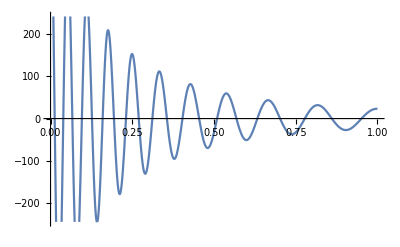

```mathematica
Plot[Re[PartialWaveuCylinder[10-0.5I,10-0.5I,tau,0.5]//FullSimplify],{tau,0,1}]
```

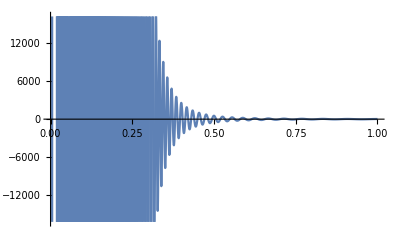

```mathematica
Plot[Re[PartialWaveuCylinder[10-0.5I,10-0.5I,0,rho]//FullSimplify],{rho,0,1}]
```